## Zestaw 1

### Zadanie 8.

Definiuję listę z żądanymi liczbami niezależnych zmiennych z rozkładu normalnego

```mathematica
n={10,10^2,10^3,10^4};
```

Definiuję CDF rozkładu, zależny od liczby niezależnych zmiennych gaussowskich

```mathematica
cdfNORmax[x_,nn_]:=CDF[NormalDistribution[0,1],x]^nn
```

Definiuję PDF ww rozkładu

```mathematica
Pmax[x_,nn_]=D[cdfNORmax[x,nn],x]
```

(2^(1/2-nn) ⅇ^(-x^2/2) nn Erfc[-x/(√2)]^(-1+nn))/(√π)

### a) Rysuję PDF rozkładu sumy N zmiennych gaussowskich

General::munfl: 0.317419^999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.317419^9999 is too small to represent as a normalized machine number; precision may be lost.

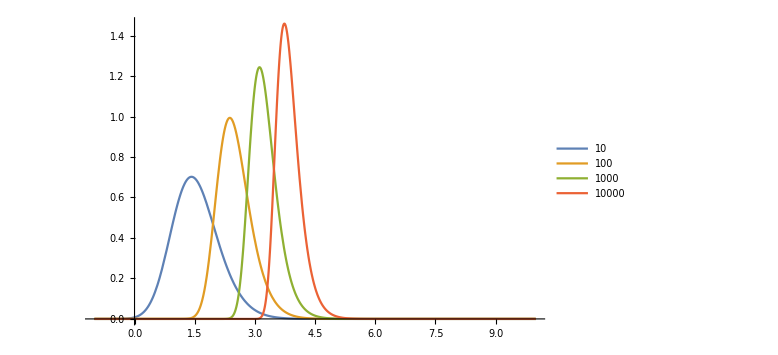

```mathematica
g=Plot[{Pmax[x,n[[1]]],Pmax[x,n[[2]]],Pmax[x,n[[3]]],Pmax[x,n[[4]]]},{x,-1,10},PlotRange->All,PlotLegends->{10,10^2,10^3,10^4},ImageSize->Large]
```

### b) Rozkład Gumbela

```mathematica
PDF[GumbelDistribution[0,1],u]
```

ⅇ^(-ⅇ^u+u)

W dalszej części wyliczam parametry a_N i b_N dla poszczególnych wartości N, tworzę rozkład Gumbela i rysuję go a na końcu pokazuję na rysunkach porównanie rozkładu Gaussa i Gumbela
Parametry a_N i b_N liczę w oparciu o rozkład normalny

#### N = 10 Wyznaczam parametry a_N i b_N

```mathematica
aN1 = InverseCDF[NormalDistribution[0,1], 1-1/n[[1]]]
```

√2 InverseErfc[1/5]

```mathematica
bN1 = InverseCDF[NormalDistribution[0,1], 1-1/(n[[1]]*E)]-aN1
```

-√2 InverseErfc[1/5]-√2 InverseErfc[2 (1-1/(10 ⅇ))]

#### Tworzę rozkład Gumbela; normalizacja w tym przypadku to podzielenie go przez b_N

```mathematica
u1[x_] = (x-aN1)/bN1;
```

```mathematica
g1[x_] = Exp[-(u1[x] + Exp[-u1[x]])]/bN1;
```

```mathematica
gu1=Plot[g1[x],{x,-5,10},PlotRange->All, PlotStyle->Red];
```

General::munfl: Exp[-236133.] is too small to represent as a normalized machine number; precision may be lost.

#### N = 100

```mathematica
aN2 = InverseCDF[NormalDistribution[0,1],1-1/n[[2]]];
```

```mathematica
bN2 = InverseCDF[NormalDistribution[0,1],1-1/(E*n[[2]])]-aN2;
```

```mathematica
u2[x_] = (x-aN2)/bN2;
```

```mathematica
g2[x_] = Exp[-(u2[x] + Exp[-u2[x]])]/bN2;
```

```mathematica
gu2=Plot[g2[x],{x,-5,10},PlotRange->All, PlotStyle->Red];
```

General::munfl: Exp[-9.80006×10^8] is too small to represent as a normalized machine number; precision may be lost.

#### N = 1000

```mathematica
aN3 = InverseCDF[NormalDistribution[0,1], 1-1/n[[3]]];
```

```mathematica
bN3 = N[InverseCDF[NormalDistribution[0,1],1-1/(E*n[[3]])]-aN3];
```

```mathematica
u3[x_] = (x-aN3)/bN3;
```

```mathematica
g3[x_] = Exp[-(u3[x] + Exp[-u3[x]])]/bN3;
```

```mathematica
gu3=Plot[g3[x],{x,-5,10},PlotRange->All, PlotStyle->Red];
```

General::munfl: Exp[-1.99131×10^12] is too small to represent as a normalized machine number; precision may be lost.

#### N = 10 000

```mathematica
aN4 = InverseCDF[NormalDistribution[0,1],1-1/n[[4]]];
```

```mathematica
bN4 = InverseCDF[NormalDistribution[0,1],1-1/(E*n[[4]])]-aN4;
```

```mathematica
u4[x_] = (x-aN4)/bN4;
```

```mathematica
g4[x_] = Exp[-(u4[x] + Exp[-u4[x]])]/bN4;
```

```mathematica
gu4=Plot[g4[x],{x,-5,10},PlotRange->All, PlotStyle->Red];
```

General::munfl: Exp[-2.69091×10^15] is too small to represent as a normalized machine number; precision may be lost.

#### Porównanie rozkładów Gaussa i Gumbela kolor NIEBIESKI oznacza rozkład Gaussowski a kolor CZERWNONY - rozkład Gumbela

Dla N = 10

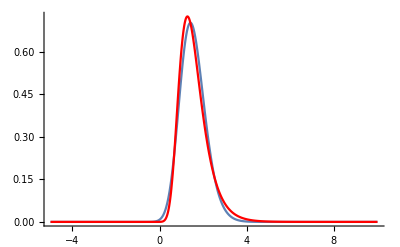

```mathematica
Show[{Plot[Pmax[x,n[[1]]],{x,-5,10},PlotRange->All],gu1}]
```

Dla N = 100

General::munfl: (5.74215×10^-7)^99 is too small to represent as a normalized machine number; precision may be lost.

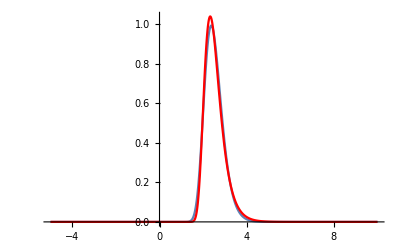

```mathematica
Show[{Plot[Pmax[x,n[[2]]],{x,-5,10},PlotRange->All],gu2}]
```

Dla N = 1000

General::munfl: (5.74215×10^-7)^999 is too small to represent as a normalized machine number; precision may be lost.

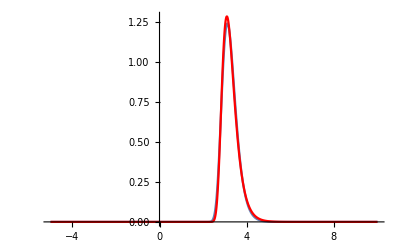

```mathematica
Show[{Plot[Pmax[x,n[[3]]],{x,-5,10},PlotRange->All],gu3}]
```

Dla N = 10 000

General::munfl: (5.74215×10^-7)^9999 is too small to represent as a normalized machine number; precision may be lost.

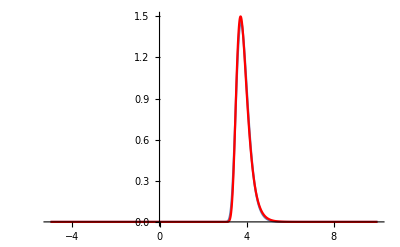

```mathematica
Show[{Plot[Pmax[x,n[[4]]],{x,-5,10},PlotRange->All],gu4}]
```

Analizując przedstawione rozkłady łatwo zauważyć, że wraz z rosnącym N dyskutowane rozkłady są sobie coraz bliższe, podczas gdy dla mniejszych N istotnie różniły się zarówno położeniem maksimum jak i kształtem ,,ogonów’’.